```mathematica
(*Turn the resdult into a list*)
sol =Solve[x^4 + 1 == 0, x];
f[r_]:=ReplaceAll[x,r];
Map[f,sol]
{-(-1)^(1/4),(-1)^(1/4),-(-1)^(3/4),(-1)^(3/4)}
(*An equivalent expression*)
x/.#&/@Solve[x^4+1 == 0]
{-(-1)^(1/4),(-1)^(1/4),-(-1)^(3/4),(-1)^(3/4)}
```

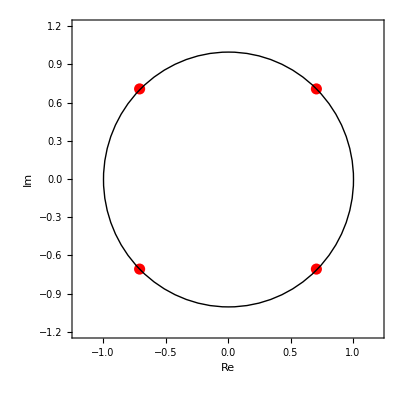

```mathematica
data=x/.#&/@Solve[x^4+1 == 0];

p=ListPlot[{Re[#],Im[#]}&/@data,AxesOrigin->{0,0},PlotRange->{{-1.2,1.2},{-1.2,1.2}},ImagePadding->40,AspectRatio->1,Frame->True,FrameLabel->{{Im,None},{Re,"complex plane"}},PlotStyle->Directive[Red,PointSize[.02]]];

Show[p,Graphics@Circle[{0,0},1]]
```